```mathematica
If[!NumberQ[makePallette],NotebookEvaluate[NotebookDirectory[]~~"visualVocabDefs.nb"],NotebookEvaluate[NotebookDirectory[]~~"vvClear.nb"]];
```

## Correlation: A Way to Find Things

```mathematica
credits
```

This notebook is part of A Visual Vocabulary for Image Processing. All rights are reserved by the authors, W. A. Sethares and C. R. Johnson, Jr. Last revised Jan 2017. All x-ray images are used with permission of the Van Gogh Museum and the Rijksmuseum, Amsterdam, The Netherlands. Please do not violate the trust of the museums that have provided access to their x-ray images by distributing this data in any form.

Correlation is a way to find patterns embedded in a large set of data.

```mathematica
TableForm[{{Hyperlink["Correlation1D",{"visualVocabCorrelation.nb","labelCorrelation1D"}],labelCorrelation1D},{Hyperlink["CorrPatterns",{"visualVocabCorrelation.nb","labelCorrPatterns"}],labelCorrPatterns},{Hyperlink["AutoCorrFind",{"visualVocabCorrelation.nb","labelAutoCorrFind"}],labelAutoCorrFind},{Hyperlink["AutoCorr1D",{"visualVocabCorrelation.nb","labelAutoCorr1D"}],labelAutoCorr1D},{Hyperlink["SigCorr",{"visualVocabCorrelation.nb","labelSigCorr"}],labelSigCorr},{Hyperlink["SigCorr2D",{"visualVocabCorrelation.nb","labelSigCorr2D"}],labelSigCorr2D}}]
```

| Calculating the correlation
 | Correlation can locate a known pattern (the marker) within a larger data set
 | Locating an unknown but repetitive marker using autocorrelation
 | The ability of autocorrelation to find the period of an unknown repetition does not depend on the shape of the signal
 | Testing the correlation between various signals
 | Correlation in 2-D operates similarly, when two signals contain the same frequencies they tend to have large correlation

The central function in the notebook is ListCorrelate[ ], which carries out all the calculations needed to correlate two sequences.

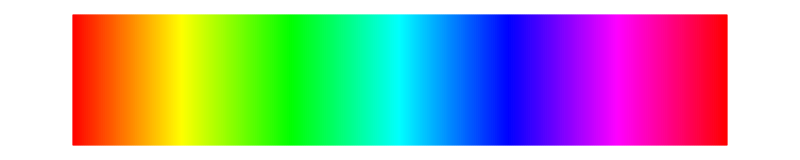

```mathematica
specLine
```

Say a known pattern of binary +/-1 numbers is embedded somewhere in a large data set. For example, the pattern of (binary) numbers highlighted in yellow might be hidden somewhere in the long stream of numbers highlighted in green. The goal is to find if the yellow sequence occurs within the data, and if so, to locate where. The figure below diagrams the method of correlation.

```mathematica
Column[{Image[-Graphics-,ImageSize->800] ,Style["Correlation can help to find a marker hidden inside a larger sequence",captionStyle]},Alignment->Center](* 1dimCorrelation.ai *)
```

-Graphics-
Correlation can help to find a marker hidden inside a larger sequence

The binary signal in green is shown with a seven-symbol embedded marker (also binary), highlighted in yellow. The process of correlation multiplies corresponding elements of the signal by the marker, and sums. The marker shifts to the right and the process repeats, creating the sequence of sums shown on the right in blue. The sum is largest when the marker is aligned with itself (because all the terms are positive, as occurs in the diagram at the shift R_(j+n)). Thus the shift with the largest correlation-sum (in this case shift j+n), is the largest term in the blue vector and points towards the embedded marker in the data sequence. The bulk of this notebook carries out this procedure in a variety of one and two dimensional settings to see how it works. In the simplest case, the marker (the yellow sequence) and the data (the green) are binary vectors.

```mathematica
specLine
```

-Graphics-

For the numerical example below, the marker is specified and the data is chosen randomly, with the marker embedded starting at the 9th location. Observe how the maximum value of the inner product (of the correlation) occurs at shift 9, which is precisely where the marker starts.

```mathematica
labelCorrelation1D="Calculating the correlation";
infoCorrelation1D="Correlation can be used to find a marker in the data.\n\nCan you see the marker in the data sequence? Regenerate the data a few times and try to guess where it is each time.\n\nShift the marker: at each shift, the inner prouct is shown in blue at the bottom. Small values mean a poor match between the data and the marker at that shift. Large values mean a good match.\n\nNote the largest value occurs at shift 9, which is where the hidden marker actually lies.\n\nThe inner product is calculated by multiplying the data sequence times the shifted marker. Since the data is binry +/-1, this just counts the number of 1's and -1's and adds the products together.\n\nClick the small + next to the slider and run this as a movie (by pressing the 'play'.";
marker12={1,1,-1,-1,1,1,1,-1,1,-1,-1,1};
insertMarker[len_,pos_,mark_]:=Flatten[{ConstantArray[0,pos-1],mark,ConstantArray[0,len-pos-Length[mark]+1]}];
data32=RandomChoice[{-1,1},32];
Manipulate[shiftMarker=insertMarker[32,p,marker12];
If[r==1,data32=Flatten[{RandomChoice[{-1,1},8],marker12,RandomChoice[{-1,1},12]}];r=0];
thisCorr32= Inner[Times,data32,shiftMarker,Plus];
Column[{ListPlot[data32,Filling->Axis,PlotStyle->Green,FillingStyle->Green,PlotLabel->"Data",AspectRatio->1/3,ImageSize->300],Spacer[10],ListPlot[shiftMarker,Filling->Axis,PlotStyle->darkYellow,FillingStyle->darkYellow,PlotLabel->"Shifted Marker",AspectRatio->1/3,ImageSize->300],Spacer[10],Text["inner product at shift "~~ToString[p]~~" is "~~ToString[thisCorr32],BaseStyle->{Blue}]}],Row[{Control[{{r,1,""},Button["Regenerate Data",r=1]&}],Spacer[20],info[infoCorrelation1D]}],{{p,1,"amount to shift"},1,Length[data32]-Length[marker12],1},FrameLabel->Style[labelCorrelation1D,Medium],TrackedSymbols->{r,p},SaveDefinitions->True]
```

```mathematica
specLine
```

-Graphics-

Next is a somewhat larger example using the same marker but a longer data sequence. Rather than outputting the blue text message "inner product at shift 9 is..." this demonstration takes the more usual path of calculating all the inner products at all the shifts, and plotting these. The message of this is clear: taking the correlation of the data with the marker is a way to locate the marker within the data since the marker starts at the index where the correlation is largest. Each time the "Regenerate Data" button is pressed, a new set of (binary) random numbers is chosen and the marker is embedded at the location specified by the "Location of Marker" slider. The correlation is taken using the ListCorrelate[ ] function and then the maximum position within the correlation vector output (the max of sums in the blue vector R_j above) is reported. In almost all cases, the reported position will be the true location.

```mathematica
labelCorrPatterns="Correlation can locate a known pattern (the marker) within a larger data set";
infoCorrPatterns="The correlation of the data with the marker is a way to locate the marker within the data.\n\nThe 'location of marker' slider lets you choose where to place the marker within the data sequence. Change this value and regenerate the data.\n\nObserve that the maximum value in the correlation occurs at the position you have chosen.\n\nCan this process ever fail to give the right answer? Can you construct a devious data sequence where it will fail. How likely is this to occur by accident? How would the answer change for different length markers?";
marker={1,1,-1,-1,1,1,1,-1,1,-1,-1,1};
data=Flatten[{RandomChoice[{-1,1},87],marker,RandomChoice[{-1,1},250-87]}];
lCorr=ListCorrelate[marker,data];
Manipulate[If[r==1,data=Flatten[{RandomChoice[{-1,1},loc-1],marker,RandomChoice[{-1,1},250-loc]}];
lCorr=ListCorrelate[marker,data];r=0];GraphicsGrid[{{ListPlot[marker,Filling->Axis,PlotStyle->darkYellow,FillingStyle->darkYellow,PlotLabel->"Marker"],ListPlot[data,Filling->Axis,PlotStyle->Green,FillingStyle->Green,PlotLabel->"Data Sequence with Embedded Marker"]},{ListPlot[Abs[lCorr],Filling->Axis,PlotLabel->"Correlation"],Text["Max Correlation\nat position "~~ToString[indMax[Abs[lCorr]]],BaseStyle->{Blue}]}},ImageSize->500],Row[{Control[{{r,1,""},Button["Regenerate Data",r=1]&}],Spacer[20],info[infoCorrPatterns]}],{{loc,87,"location of marker"},1,200,1,Appearance->"Labeled"},FrameLabel->Style[labelCorrPatterns,Medium],TrackedSymbols->{r,loc},SaveDefinitions->True]
```

HW: How often would you expect the marker sequence to accidentally appear in the random data sequence? Does this depend on how long the marker is?  Does this depend on how much data there is?

Correlation can often be useful when the data is not binary and even when it is noisy, that is, the same basic procedure works for grayscale (and not just binary 1/-1 data).

HW: Create a simulation like that above where the marker and the data are chosen from (real) numbers between -1 and 1. How reliable is the pattern-finding in this case? Hint: if you are getting lots of mismatches in reporting of the location, try making the marker sequence longer.

```mathematica
specLine
```

-Graphics-

The same basic procedure works in multiple dimensions. For example, a neighborhood-three correlation (as shown below) can be defined by 9 numbers centered on w(0,0) and labeled w(i,j), for i=-1,0,1 and j=-1,0,1. The correlation process at a point (x,y) consists of multiplying w(-1,-1) and f(x-1,y-1), w(-1,0) and f(x-1,y), w(-1,1) and f(x-1,y+1), and so on for all 9 colored pairs. These nine products are then summed together to give a single number which is the value g(x,y) that output image assumes at the point (x,y). The correlation then moves on to the next location, repeating the procedure for every point in the image. This process is almost the same as the linear filter, though the terms in a linear filter are rearranged from the correlation.

```mathematica
Labeled[Image[-Graphics-,ImageSize->425], 
  "The correlation of a 3 by 3 mask w( ) with an image f( )", 
  LabelStyle->captionStyle](* 2dimCorrelation.ai *)
```

-Graphics-The correlation of a 3 by 3 mask w( ) with an image f( )

The output pixel value g(x,y) is thus a sum of products. In full detail 

g(x,y) = w(-1,-1) f(x-1,y-1) + w(-1,0) f(x-1,y) + w(-1,1) f(x-1,y+1) + w(0,-1) f(x,y-1) + w(0,0) f(x,y) + w(-1,1) f(x,y+1) + w(1,-1) f(x+1,y-1) + w(1,0) f(x+1,y) + w(1,1) f(x+1,y+1)

and the process is repeated for every location (x,y) in the image.

Given how unwieldy the expression is, it might seem as if this would be painful to implement and difficult to understand. But no. Mathematica (and other high level computational languages) have simple-to-invoke commands that implement this quickly and efficiently and with little fuss.

```mathematica
specLine
```

-Graphics-

ListCorrelate[ ] works in two dimensions as easily as in one. Here is a thread x-ray (a two centimeter square patch from F634) in which several copies of the tiny letter "A" are embedded.

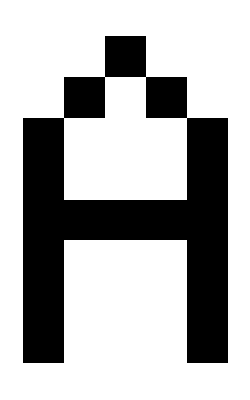
-Graphics-Many copies of the letter "A" are superimposed on the middle image to form the image on the right

```mathematica
maskA={{-1,-1, 1,-1,-1},{-1, 1,-1, 1,-1},{1,-1,-1,-1, 1},
{1,-1,-1,-1, 1},{1,1,1,1,1},{1,-1,-1,-1, 1},{1,-1,-1,-1, 1},
{1,-1,-1,-1, 1}};
threadImage=allImagesXray[[f634Tile]];
threadMat = ImageData[threadImage];
dims=ImageDimensions[threadImage];
randInt = RandomInteger[{10,dims[[1]]-10},30];
Table[threadMat[[randInt[[i]];;randInt[[i]]+7,randInt[[i+1]];;randInt[[i+1]]+4]] = maskA;,{i,1,29,2}];
Labeled[GraphicsRow[{ArrayPlot[maskA+1],threadImage, Image[threadMat]},ImageSize->Large],"Many copies of the letter \"A\" are superimposed on the middle image to form the image on the right",LabelStyle->captionStyle]
```

It is pretty hard to see the A’s embedded in the right hand picture above. By correlating with the known shape, it is possible to highlight the locations where the A’s occur.

```mathematica
lCorr2D = ListCorrelate[maskA,threadMat];
clipCorr = Clip[lCorr2D,{Max[lCorr2D]-5,Max[lCorr2D]}];
clipCorr = clipCorr-Min[clipCorr];
Labeled[ImageFilter[Max,Image[clipCorr,ImageSize->300],3],"Correlation shows the location of the hidden A's",LabelStyle->captionStyle]
```

-Graphics-Correlation shows the location of the hidden A's

Searching for collections of +/-1’s and for the letter A might seem a bit frivolous. There are other (potentially more useful) things to search for in both 1D and 2D.

```mathematica
specLine
```

-Graphics-

For example, suppose that there is a repetitive shape and the goal is to find the period of the repetition. Say the shape is a length-50 sequence and this shape is embedded in a longer noisy sequence every 100 elements (these are the default values in the following demonstration). Even though there is a lot of repetition, it is not at all clear visually -- in fact, the whole plot (on the left) looks quite random. One possibility would be to search for the length-50 sequence exactly as we searched for the marker sequence above. Of course, this would work fine, but it requires that we know the values of the sequence we are searching for. What if we don’t know the detailed shape or form of the repetitive segment? In this case, it is still possible to correlate the sequence with itself, which can help to uncover repetitive patterns or subsequences even when the structure and placement of the pattern is unknown. This is called autocorrelation.

```mathematica
labelAutoCorrFind="Locating an unknown but repetitive marker using autocorrelation";
infoAutoCorrFind="Correlating a sequence with itself (i.e., autocorrelation) can help to uncover repetitive patterns or subsequences even when the structure and placement of the pattern is unknown.\n\nUsing the default values, the peaks in the autocorrelation occur at 101, 201, 301, etc., indicating that the (unknown) pattern occurs every 100 elements in the sequence.\n\nIncreasing or decreasing the pattern spacing causes the peaks to spread out or squish in correspondingly.\n\nChange the pattern width. Longer patterns are detected more easily (there is more separation between the peaks and the noise in the autocorrelation). Shorter patterns are more difficult to discern, and if the pattern is too short, it becomes lost in the noise.";
Manipulate[
repet=RandomVariate[UniformDistribution[],patWidth];
seq=RandomVariate[UniformDistribution[],1000];
Do[seq[[n;;n+patWidth-1]]=repet,{n,30,1000-patWidth,patSpacing}];
autoCorr=ListCorrelate[seq,seq,1];GraphicsRow[{ListPlot[seq,PlotRange->All,PlotLabel->"Repetitive pattern embedded in noise"],ListPlot[Rest[autoCorr],PlotRange->All,PlotLabel->"Peaks in autocorrelation locates pattern"]},ImageSize->600],
Row[{Control[{{patWidth,50,"pattern width"},5,100,1,Appearance->"Labeled"}],Spacer[20],info[infoAutoCorrFind]}],Control[{{patSpacing,100,"pattern spacing"},30,200,1,Appearance->"Labeled"}],FrameLabel->Style[labelAutoCorrFind,Medium],TrackedSymbols->{patWidth,patSpacing},SaveDefinitions->True]
```

```mathematica
specLine
```

-Graphics-

Another place where autocorrelation can be useful is in locating small (but repetitive) signals in noise. Even though is pretty hard to “see” the signal buried inside noise, autocorrelation can often make it considerably clearer. It is much easier to count the undulations in the autocorrelation than in the noisy signal itself. Counting over the length of the signal corresponds exactly to the frequency of the sine wave. More common would be to look at the first place (other than zero) where a maximum is achieved: for the default parameters this is about 333. Since there are 1000 samples in the full length, this corresponds to the “unknown” frequency 3 (=1000/333). The vertical axis is large because the sum is taken over the whole sequence.

```mathematica
labelAutoCorr1D="The ability of autocorrelation to find the period of an unknown repetition does not depend on the shape of the signal";
infoAutoCorr1D="Noise is superimposed on a perodic signal with frequency specified by the slider.\n\nThe basic shape of the period is specified by the chooser box.\n\nThe autocorrelation always has largest value at shift 0 (at the left).\n\nThe location of the next largest peak is an estimate of the underlying period of the signal.\n\nAs the frequency increases, the estimated period decreases (and vice versa).\n\nTry looking at a 'movie' by animating the frequency.";
Manipulate[smallSin=Table[a waveshape[f t]+RandomVariate[NormalDistribution[]],{t,0,1,0.001}];autoCorr=ListCorrelate[smallSin,smallSin,1];
GraphicsRow[{ListLinePlot[smallSin,PlotLabel->"signal"],ListLinePlot[autoCorr,PlotLabel->"autocorrelation of the signal"]},ImageSize->600],
Row[{Control[{{a,10,"amplitude"},0,10,Appearance->"Labeled"}],Spacer[20],Control[{{f,3,"frequency"},1,10,Appearance->"Labeled"}]}],
Row[{Control[{{waveshape,TriangleWave,"wave shape"},{TriangleWave,SawtoothWave,SquareWave}}],Spacer[20],info[infoAutoCorr1D]}],FrameLabel->Style[labelAutoCorr1D,Medium],TrackedSymbols->{a,f,waveshape},SaveDefinitions->saveDef]
```

HW: Choose frequency 8.5 and the triangle waveshape. Observe that the autocorrelation dies away to near zero in the middle. Explain why this happens whenever the frequency is halfway between an integer value.

The ability of autocorrelation to find the period of the unknown repetition is striking, and does not depend on the exact shape of the signal. Indeed, the above simulation allows three choices of wave shape, and the behavior is similar in all three cases. If the amplitude of the repetitive wave falls too low however, the method will fail.

The ListCorrelate[ ] function that is used throughout this notebook has a number of options, some of which specify how to handle end conditions. For example, in the pattern finding case (of 1D correlation) it does not make sense to have the yellow marker look for the pattern outside the boundaries of the green data sequence; this condition is with no zero-padding of the sequences. In the case of autocorrelation, the sequence is “padded circularly”  (to replace missing values with corresponding values from the opposite end of the sequence). In yet other situations (such as the crosscorrelation below), it is simplest to pad zeros onto both the front and end of the kernel and signal whenever needed. More details about these options can be found here.

```mathematica
specLine
```

-Graphics-

Here correlation is applied to two different signals and is used as a way to measure how close (or how similar) the two sequences are.

```mathematica
labelSigCorr="Testing the correlation between various signals";
infoSigCorr="Select two signals from the chooser boxes. One is called the 'kernel' (left plot) and the other is called the 'signal' (middle plot). The cross correlation is shown in the right plot.\n\nObserve that the order of the signals is irrelevant: for example, the cross-correlation between a pulse train and single pulse is the same as the cross correlation between a single pulse and the pulse train.\n\nObserve that the two noise signals do not correlate well with any signal (other than themselves).\n\nObserve that the square and the triangle correlare almost as well as the square with itself (this is because they have the same basic period).\n\nAny signal crosscorrelated with a pulse gives back the signal.\n\nSet both kernel and signal to triangle waves. Can you explain why the signal looks different than when doing the autocorrelation of the triangle wave (in the previous demonstration)? (Hint: it's got to do with the padding of the end conditions).";Manipulate[GraphicsRow[{ListLinePlot[allSigs[[kernel]],Filling->Axis,PlotLabel->"Kernel: "~~sigNames[[kernel]]],ListLinePlot[allSigs[[signal]],Filling->Axis,PlotLabel->"Signal: "~~sigNames[[signal]]],ListLinePlot[ListCorrelate[allSigs[[kernel]],allSigs[[signal]],{-1,1},{0,0}],Filling->Axis,PlotLabel->"Cross-Correlation",PlotRange->All]},ImageSize->850],Row[{Control[{{kernel,5,""},Thread[Range[numSigs]->sigNames],ControlType->SetterBar}],Spacer[10],Control[{{signal,7,""},Thread[Range[numSigs]->sigNames],ControlType->SetterBar}],Spacer[10],info[infoSigCorr]}],FrameLabel->Style[labelSigCorr,Medium],TrackedSymbols->{signal,kernel},SaveDefinitions->True]
```

A collection of different signals appear above along with their correlations. When a train of pulses is correlated with a single pulse, the correlation reproduces the pulse once for each spike. When the pulse is correlated with a sinusoid, the correlation smears the pulse and inverts it with each undulation. When two different random signals are correlated, the output is modestly sized (and pretty random) because the two random sequences were chosen independently. Notice that when a random noise signal is correlated with itself, there is a large spike in the middle, indicated the shift j where the sequence is perfectly aligned with itself. Try these out (and more) above. Observe that when x=y (i.e., the kernel and the signal are the same), the largest value of the correlation occurs at a shift j=0. In the examples that are periodic, note that the distance between successive peaks of the correlation is directly related to the periodicity in the input.

```mathematica
specLine
```

-Graphics-

Of course, correlation also can be used in two dimensions, and the formula is just two independent copies of the one-dimensional formula. There are now two shift parameters i and j in two directions, and the sum is taken over all shifts in both directions. At any point {s,t} the cross correlation is:

R_xy[s,t]=∑_(i=-∞)^∞ ∑_(j=-∞)^∞ x[i,j] y[s+i,t+j]

```mathematica
labelSigCorr2D="Correlation in 2-D operates similarly, when two signals contain the same frequencies they tend to have large correlation";
infoSigCorr2D="This follows the same plan as the previous demonstration, but in 2D instead of 1D. Choose two signals/images (displayed in the left and middle). The cross-correlation is shown in the rightmost image and the normalized cross-correlation value is displayed numerically.\n\nObserve that any signal correlated with itself gives a large value (which appears in the correlation image as a white dot in a black field).\n\nTry changing the horizontal and vertical frequencies of the 2D sinusoidal image. This does not change the correlation between the two sinewave images singificantly (because they are both the same).\n\nChoose the thread image on the left and the 2D sine image on the right. Change the two frequency sliders so as to maximize the correlation. This is the sine wave that correlates best with the thread image.";
sigNames2D={"2D Sines A","2D Sines B","Thread","Noise1","Noise2"};
numSigs2D=Length[sigNames2D];
sig2D3=ImageData[ColorNegate[Import[pathXray~~"F634Tile.tif"]]][[1;;100,1;;100]];
sig2D4=RandomVariate[UniformDistribution[{0,1}],{100,100}];
sig2D5=RandomVariate[UniformDistribution[{0,1}],{100,100}];
Manipulate[Module[{x,y,s,r,rxy,normalizedRxy},s=Table[Sin[2 Pi fh t],{t,0,1,0.01}];
r=Table[Sin[2 Pi fv t],{t,0,1,0.01}];
sig2D1=Outer[Plus,r,s];
sig2D2=Outer[Times,r,s];
allSigs2D={sig2D1,sig2D2,sig2D3,sig2D4,sig2D5};
numSigs2D=Length[allSigs2D];
x=allSigs2D[[kernel]];y=allSigs2D[[signal]];
rxy=ListCorrelate[x-Mean[x],y-Mean[y],{-1,1},{0,0}];
normalizedRxy=Max[rxy-Mean[rxy]]/(Norm[x-Mean[x],1] Norm[y-Mean[y],1]);
GraphicsRow[{Image[x],Image[y],ImageAdjust[Image[rxy]],Style[normalizedRxy,Medium]},ImageSize->800]],Row[{Control[{{kernel,1,""},Thread[Range[numSigs2D]->sigNames2D],ControlType->SetterBar}],Spacer[10],Control[{{signal,4,""},Thread[Range[numSigs2D]->sigNames2D],ControlType->SetterBar}],Spacer[20],info[infoSigCorr2D]}],Row[{Control[{{fh,4,"horizontal frequency"},1,10}],Spacer[10],Control[{{fv,4,"vertical frequency"},1,10}]}],FrameLabel->Style[labelSigCorr2D,Medium],TrackedSymbols->{signal,kernel,fh,fv},SaveDefinitions->True]
```

HW: Can you use the vertical and horizontal frequency sliders to make the cross correlation between the thread tile and a 2D sinusoid look like the autocorrelation between the thread tile and itself.

The final column shows the maximum correlation value, normalized by the magnitudes of the signals. This makes it easier to see what "large" and "small" mean: numbers near zero mean the images are effectively unrelated, while numbers around unity indicate that they share significant similarities. For example, when correlating noises -- if the noises are different then the normalized correlation is small. If the noises are actually the same (for instance, choose Noise1 for both signals), the correlation becomes larger. Try correlating the thread image with the 2D sinusoidal models. By playing with the frequency of the sine waves, it is possible to increase (or decrease) the correlation, indicating that the thread image is more like certain frequencies of sinusoids than others. Which of the two sinusoidal models matches the thread image best? What values did you find?

More examples of the uses of correlation and autocorrelation in the application of correlation methods to the thread counting problem.